```mathematica
alphaRod = 0.02;
```

```mathematica
valsA = NDSolveValue[{D[u[x,t],t]-alphaRod*Laplacian[u[x,t],{x}]==0,DirichletCondition[u[x,t]==20*x^2*(x-1)^2,t==0]},u,{x,0,1},{t,0,10}]
```

NDSolveValue::femcscd: The PDE is convection dominated and the result may not be stable. Adding artificial diffusion may help.

InterpolatingFunction[{{0., 1.}, {0., 10.}}, <>]

```mathematica
epsilon = 0.1;
```

```mathematica
diff[x_]:=Piecewise[{{0.02, x < 0.5-epsilon},{0.8,x ≥ 0.5-epsilon && x < 0.5 + epsilon},{0.02,x≥0.5+epsilon}}];
```

```mathematica
vals2A = NDSolveValue[{D[u[x,t],t]-diff[x]*Laplacian[u[x,t],{x}]==0,DirichletCondition[u[x,t]==20*x^2*(x-1)^2,t==0]},u,{x,0,1},{t,0,10}]
```

NDSolveValue::femcscd: The PDE is convection dominated and the result may not be stable. Adding artificial diffusion may help.

InterpolatingFunction[{{0., 1.}, {0., 10.}}, <>]

```mathematica
Manipulate[Plot[{vals2A[x,t],valsA[x,t],0,1.2},{x,0,1}],{t,0,10}]
```

```mathematica
uVals = NDSolveValue[{D[u[x,t],t]-alphaRod*Laplacian[u[x,t],{x}]==0,DirichletCondition[u[x,t]==20*x^2*(x-1)^2,t==0]},u,{x,0,0.5-epsilon},{t,0,10}]
```

NDSolveValue::femcscd: The PDE is convection dominated and the result may not be stable. Adding artificial diffusion may help.

InterpolatingFunction[{{0., 0.4}, {0., 10.}}, <>]

```mathematica
uValsDx[x_,t_]:= D[uVals[xx,tt],xx]/.{xx->x,tt->t};
```

```mathematica
uValsDt[x_,t_]:= D[uVals[xx,tt],tt]/.{xx->x,tt->t};
```

```mathematica
Clear[x]; Clear[t]
```

```mathematica
vVals = NDSolveValue[{D[u[x,t],t]-0.1*Laplacian[u[x,t],{x}]== NeumannValue[uValsDx[x,t],x==0.5-epsilon],
DirichletCondition[u[x,t]==uVals[x,t],x==0.5-epsilon],DirichletCondition[u[x,t]==20*x^2*(x-1)^2,t==0]},u,{x,0.5-epsilon,0.5+epsilon},{t,0,10}]
```

NDSolveValue::femcscd: The PDE is convection dominated and the result may not be stable. Adding artificial diffusion may help.

InterpolatingFunction[{{0.4, 0.6}, {0., 10.}}, <>]

```mathematica
diff2[x_]:=Piecewise[{{0.02, x < 0.5-epsilon},{0.1,x ≥ 0.5-epsilon && x < 0.5 + epsilon},{0.02,x≥0.5+epsilon}}];
```

```mathematica
vals2B = NDSolveValue[{D[u[x,t],t]-diff2[x]*Laplacian[u[x,t],{x}]==0,DirichletCondition[u[x,t]==20*x^2*(x-1)^2,t==0]},u,{x,0,1},{t,0,10}]
```

NDSolveValue::femcscd: The PDE is convection dominated and the result may not be stable. Adding artificial diffusion may help.

InterpolatingFunction[{{0., 1.}, {0., 10.}}, <>]

```mathematica
vVals2 = NDSolveValue[{D[u[x,t],t]-0.1*Laplacian[u[x,t],{x}]==0,DirichletCondition[u[x,t]==uVals[x,t],x==0.5-epsilon],DirichletCondition[u[x,t]==20*x^2*(x-1)^2,t==0]},u,{x,0.5-epsilon,0.5+epsilon},{t,0,10}]
```

NDSolveValue::femcscd: The PDE is convection dominated and the result may not be stable. Adding artificial diffusion may help.

InterpolatingFunction[{{0.4, 0.6}, {0., 10.}}, <>]

```mathematica
Manipulate[Plot[{
Piecewise[{{uVals[x,t],x≤0.5-epsilon},{vVals2[x,t],x>0.5-epsilon}}],Piecewise[{{uVals[x,t],x≤0.5-epsilon},{vVals[x,t],x>0.5-epsilon}}],0,1.2},{x,0,0.5+epsilon},PlotLegends->"Expressions"],{t,0,10}]
```

```mathematica
Manipulate[Plot[{vals2B[x,t],
Piecewise[{{uVals[x,t],x≤0.5-epsilon},{vVals2[x,t],x>0.5-epsilon}}],Piecewise[{{uVals[x,t],x≤0.5-epsilon},{vVals[x,t],x>0.5-epsilon}}],0,1.2},{x,0,0.5+epsilon},PlotLegends->"Expressions"],{t,0,10}]
```

```mathematica
(*
Conclusions so far:
Boundary conditions do not seem too necessary in modelling heat diffusion. 
Using Neumann conditions and not using them did not make a huge difference i.e. using vVals versus vVals2 above. 
There is a large different though between one system with different diffusion constants and two systems with matched boundary conditions. *)
```

```mathematica
totalEnergy[t_]:=Integrate[vals2A[x,t],{x,0,1}]
```

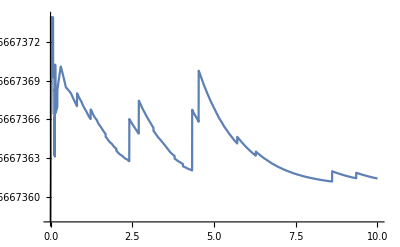

```mathematica
Plot[totalEnergy[t],{t,0,10}]
```

```mathematica
vals2Aderiv[x_,t_]:= D[vals2A[xx,tt],tt]/.{xx->x,tt->t};
```

```mathematica
valsAderiv[x_,t_]:=D[valsA[xx,tt],tt]/.{xx->x,tt->t};
```

```mathematica
Manipulate[Plot[{vals2Aderiv[x,t],valsAderiv[x,t],0,1.2},{x,0,1}],{t,0,10}]
```

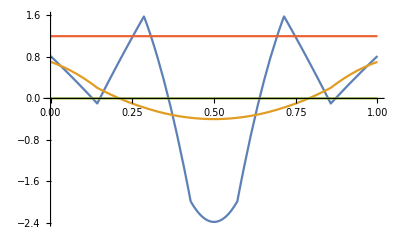
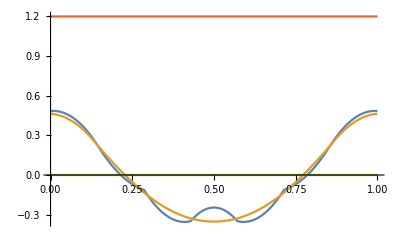
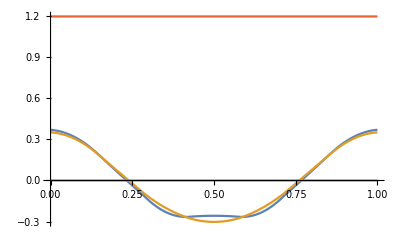
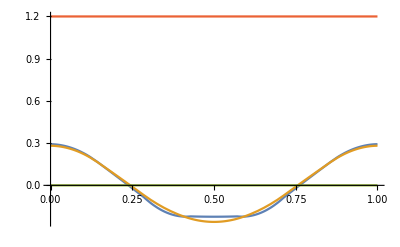
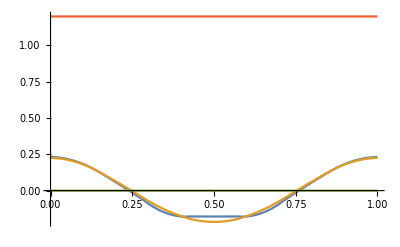
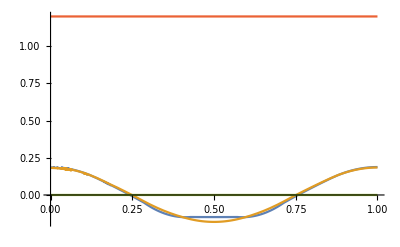
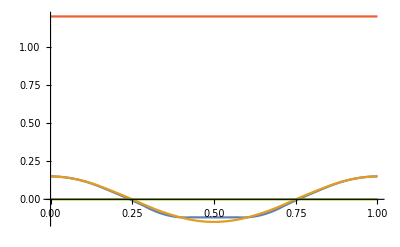
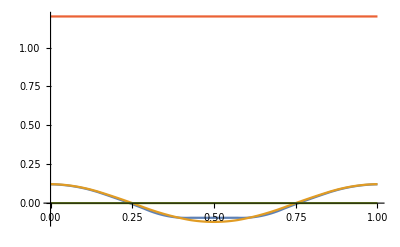

```mathematica
Table[Plot[{vals2Aderiv[x,t],valsAderiv[x,t],0,1.2},{x,0,1}],{t,0,4,.25}]
```

```mathematica
valsAderivX[x_,t_]:=D[valsA[xx,tt],xx]/.{xx->x,tt->t};vals2AderivX[x_,t_]:= D[vals2A[xx,tt],xx]/.{xx->x,tt->t};
```

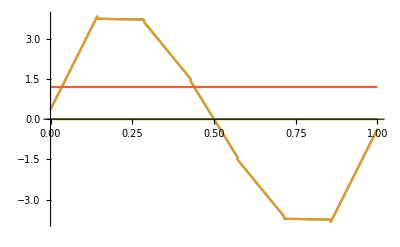
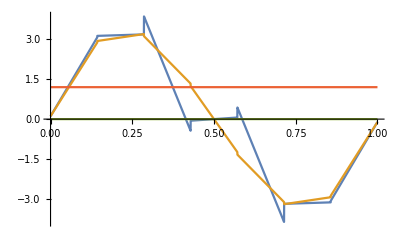
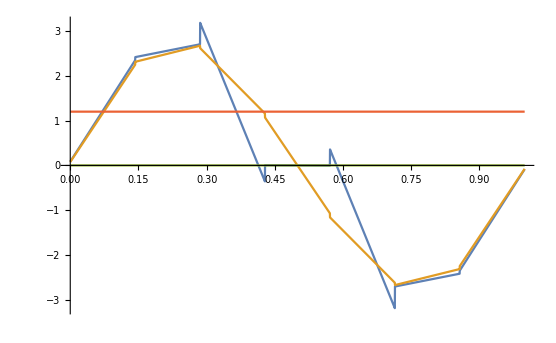
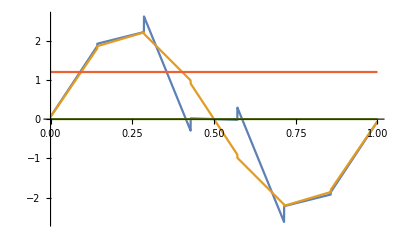
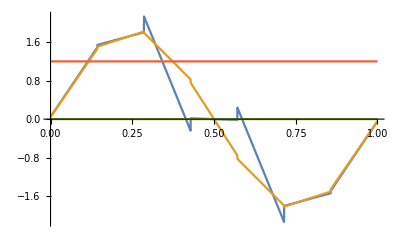
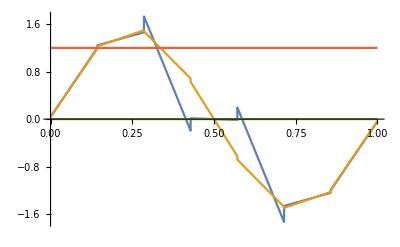
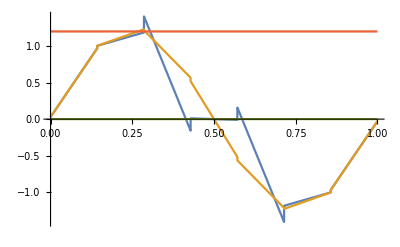
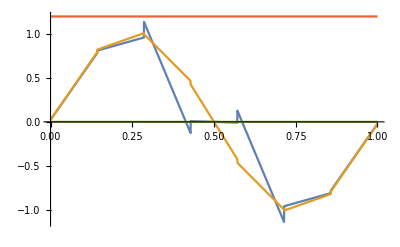

```mathematica
Table[Plot[{vals2AderivX[x,t],valsAderivX[x,t],0,1.2},{x,0,1}],{t,0,4,.25}]
```

```mathematica
vals2A = NDSolveValue[{D[u[x,t],t]-diff[x]*Laplacian[u[x,t],{x}]==0,DirichletCondition[u[x,t]==-20*x*(x-1),t==0]},u,{x,0,1},{t,0,10}]
```

NDSolveValue::femcscd: The PDE is convection dominated and the result may not be stable. Adding artificial diffusion may help.

InterpolatingFunction[{{0., 1.}, {0., 10.}}, <>]

```mathematica
Manipulate[Plot[{vals2A[x,t],valsA[x,t],0,1.2},{x,0,1}],{t,0,10}]
```